```mathematica
1/365
```

1/365

```mathematica
N[1/365]
```

0.00273973

```mathematica
Quantity[1000000000,"Seconds"]
```

1000000000 s

```mathematica
UnitConvert[Quantity[1000000000,"Seconds"],MixedUnit[{"Years","Months","Days","Hours","Minutes","Seconds"}]]
```

31 8

```mathematica
Quantity[1000000,"Seconds"]
```

1000000 s

```mathematica
UnitConvert[Quantity[1000000,"Seconds"],MixedUnit[{"Days","Hours","Minutes","Seconds"}]]
```

11 13

```mathematica
Quantity[300,"Megabits"]
```

300 Mb

```mathematica
UnitConvert[Quantity[300,"Megabits"],"Megabytes"]
```

75/2 MB

```mathematica
N[Quantity[75/2,"Megabytes"]]
```

37.5 MB

```mathematica
NormalDistribution[]
```

NormalDistribution[0,1]

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

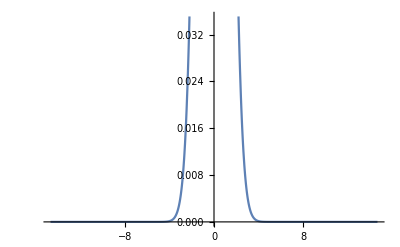

```mathematica
Plot[(ⅇ^(-x^2/2))/(√(2 π)),{x,-14.696938456699069,14.696938456699069}]
```

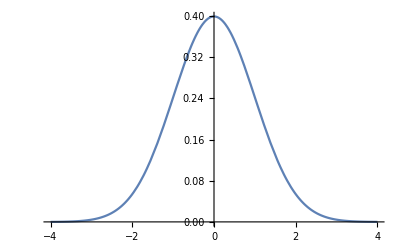

```mathematica
Plot[(ⅇ^(-x^2/2))/(√(2 π)),{x,-4,4},PlotRange->Full]
```

```mathematica
Skewness@((ⅇ^(-x^2/2))/(√(2 π)))
```

Skewness[(ⅇ^(-x^2/2))/(√(2 π))]

```mathematica
Skewness@NormalDistribution[]
```

0

```mathematica
StudentTDistribution[0]
```

StudentTDistribution[0]

```mathematica
ChiSquareDistribution[0]
```

ChiSquareDistribution[0]

```mathematica
ChiSquareDistribution[1]
```

ChiSquareDistribution[1]

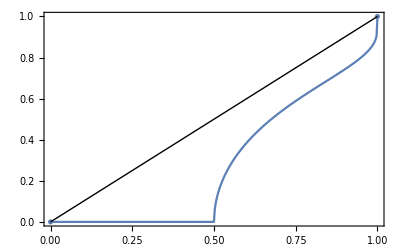

```mathematica
ProbabilityPlot[ChiSquareDistribution[1]]
```

```mathematica
Skewness@ChiSquareDistribution[1]
```

2 √2

```mathematica
Kurtosis@ChiSquareDistribution[1]
```

15

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
Quartiles[RandomVariate[NormalDistribution[],10]]
```

{-0.64962,0.0486858,0.503976}

```mathematica
Quartiles[RandomVariate[NormalDistribution[],10000]]
```

{-0.681451,-0.0133597,0.653434}

```mathematica
amzn = FinancialData["NASDAQ:AMZN","Price",All]
```

TimeSeries[…]

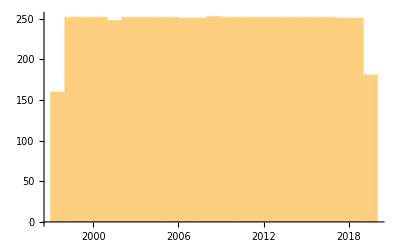

```mathematica
DateHistogram[amzn]
```

```mathematica
Map[Total,Partition[Differences@amzn["Values"],5]]
```

{-0.56 $,0.10 $,0.16 $,-0.07 $,-0.06 $,-0.04 $,0.51 $,0.14 $,0.05 $,0.14 $,-0.01 $,0.02 $,-0.29 $,0.18 $,0.13 $,0.89 $,0.11 $,1.27 $,-0.29 $,-0.28 $,-0.08 $,0.45 $,0.52 $,0.01 $,-1.01 $,0.47 $,-0.21 $,0.16 $,0.15 $,-0.12 $,0.21 $,0.36 $,-0.63 $,0.46 $,0.02 $,0.38 $,-0.34 $,0.29 $,0.26 $,0.57 $,0.95 $,-0.27 $,0.36 $,0.11 $,-0.02 $,0.91 $,-0.74 $,0.69 $,-0.43 $,0.21 $,-0.35 $,-0.22 $,0.15 $,3.10 $,1.57 $,4.52 $,3.84 $,-3.77 $,3.39 $,0.74 $,-2.23 $,0.85 $,1.13 $,1.16 $,-3.97 $,-3.27 $,-2.09 $,1.97 $,5.02 $,-1.60 $,-2.14 $,2.09 $,1.94 $,2.27 $,-0.69 $,-0.10 $,15.29 $,-1.42 $,-0.91 $,6.45 $,13.27 $,-0.19 $,25.90 $,-10.44 $,-7.50 $,-3.03 $,-0.53 $,-5.69 $,1.00 $,13.25 $,-5.41 $,8.38 $,-3.47 $,8.81 $,16.63 $,-2.25 $,-3.19 $,16.94 $,-31.44 $,2.69 $,-7.88 $,-10.53 $,0.28 $,0.94 $,-1.16 $,3.03 $,3.69 $,-0.31 $,7.53 $,-16.19 $,-2.81 $,-2.16 $,-2.75 $,7.19 $,12.19 $,-5.19 $,6.44 $,-2.69 $,1.19 $,12.25 $,12.00 $,-14.19 $,3.56 $,-8.00 $,-5.69 $,10.00 $,3.00 $,12.50 $,-2.69 $,14.75 $,-5.50 $,-14.69 $,0.06 $,-15.75 $,0.19 $,-2.00 $,10.87 $,4.06 $,-9.06 $,-2.25 $,-5.88 $,6.25 $,-2.56 $,1.44 $,-1.19 $,-2.25 $,-14.94 $,3.06 $,2.81 $,3.12 $,-4.56 $,-1.13 $,-6.13 $,8.00 $,-6.06 $,-3.13 $,-11.38 $,3.06 $,-2.19 $,7.44 $,-4.63 $,-7.38 $,2.69 $,4.63 $,-1.06 $,3.13 $,6.25 $,-3.44 $,-4.94 $,0.38 $,-1.88 $,-8.19 $,-2.69 $,6.75 $,5.50 $,-3.50 $,-4.38 $,-4.31 $,-0.50 $,-3.31 $,1.31 $,-7.50 $,0.38 $,-0.63 $,3.13 $,0.88 $,0.00 $,-3.13 $,-2.06 $,-1.81 $,-1.75 $,2.06 $,-1.63 $,-0.63 $,0.80 $,-2.40 $,4.92 $,2.67 $,-0.56 $,1.26 $,-2.07 $,0.16 $,1.97 $,0.20 $,-1.25 $,-3.21 $,-0.09 $,1.75 $,1.66 $,0.20 $,0.02 $,-3.48 $,-0.65 $,-1.78 $,0.28 $,-0.27 $,-1.54 $,-1.10 $,-0.03 $,-1.45 $,1.11 $,1.76 $,-0.11 $,-1.74 $,-0.04 $,0.06 $,2.19 $,2.24 $,0.45 $,0.31 $,-1.38 $,0.24 $,0.80 $,-0.86 $,-1.30 $,4.70 $,-0.71 $,-1.21 $,0.89 $,0.32 $,2.75 $,0.23 $,-1.70 $,-0.27 $,-0.49 $,-0.65 $,0.41 $,0.05 $,2.63 $,-0.58 $,2.70 $,-0.05 $,0.15 $,-0.92 $,-0.91 $,1.22 $,-2.45 $,-1.60 $,1.30 $,0.00 $,-3.06 $,1.67 $,-0.26 $,0.72 $,1.11 $,-0.56 $,0.14 $,1.30 $,-0.75 $,1.15 $,-0.46 $,1.91 $,0.58 $,0.26 $,0.50 $,-0.29 $,2.70 $,1.78 $,0.12 $,-2.43 $,0.83 $,-0.27 $,-3.35 $,2.13 $,1.25 $,-0.48 $,0.03 $,0.27 $,-2.03 $,1.72 $,0.23 $,0.96 $,1.74 $,3.15 $,-0.68 $,-0.96 $,-0.47 $,-0.50 $,3.86 $,0.85 $,1.74 $,-0.14 $,3.29 $,0.38 $,-1.16 $,1.77 $,-0.44 $,1.85 $,3.25 $,-2.82 $,2.43 $,0.55 $,-1.72 $,1.27 $,3.55 $,2.12 $,1.41 $,-2.10 $,2.70 $,2.16 $,0.04 $,7.77 $,2.05 $,-5.59 $,1.51 $,-0.84 $,-0.19 $,-5.95 $,5.12 $,-2.41 $,-0.57 $,-1.75 $,4.23 $,-0.44 $,1.88 $,1.29 $,-4.24 $,-6.57 $,1.75 $,-2.49 $,-1.00 $,0.74 $,-3.11 $,1.73 $,-1.02 $,2.75 $,3.36 $,-2.60 $,0.79 $,-2.69 $,-1.70 $,1.15 $,-1.88 $,7.33 $,3.26 $,-1.65 $,-1.11 $,4.71 $,-2.71 $,-0.60 $,-5.64 $,-6.79 $,-0.85 $,-0.56 $,2.80 $,0.94 $,-2.06 $,-0.17 $,4.50 $,-0.74 $,-0.97 $,0.29 $,-2.05 $,0.37 $,-5.02 $,2.46 $,1.92 $,1.54 $,-1.28 $,1.00 $,-1.04 $,0.96 $,2.24 $,2.27 $,-2.68 $,2.74 $,-3.64 $,1.54 $,-6.18 $,-0.16 $,-2.00 $,1.36 $,-0.10 $,-1.53 $,-0.69 $,1.09 $,0.63 $,-0.93 $,-0.24 $,-1.21 $,1.44 $,-0.11 $,1.74 $,-0.14 $,0.14 $,-0.64 $,0.36 $,-0.29 $,-2.11 $,2.68 $,1.60 $,0.76 $,6.98 $,0.73 $,-0.62 $,-1.27 $,-0.98 $,0.83 $,0.31 $,-2.06 $,1.29 $,1.77 $,-1.53 $,1.25 $,2.35 $,-6.63 $,1.58 $,2.50 $,4.40 $,-0.39 $,0.37 $,0.58 $,-0.44 $,-0.98 $,-0.12 $,-3.47 $,-0.67 $,1.23 $,-7.01 $,0.47 $,-0.13 $,-0.85 $,-0.51 $,-0.02 $,-0.99 $,0.10 $,0.75 $,-0.71 $,0.83 $,-0.54 $,-1.96 $,-0.23 $,-2.55 $,3.58 $,-0.12 $,-1.52 $,1.41 $,1.89 $,1.67 $,-2.41 $,-3.19 $,0.27 $,-6.02 $,0.12 $,-1.22 $,3.05 $,-1.09 $,3.73 $,-0.97 $,1.29 $,-0.29 $,-0.92 $,2.61 $,-0.88 $,0.28 $,5.27 $,0.06 $,1.78 $,2.45 $,-1.52 $,-1.94 $,-0.52 $,0.96 $,0.87 $,-1.92 $,-0.17 $,-1.25 $,0.48 $,-0.27 $,1.69 $,2.66 $,-2.68 $,-0.25 $,-0.76 $,0.76 $,0.79 $,1.82 $,0.49 $,3.31 $,11.82 $,4.37 $,1.67 $,0.37 $,5.78 $,0.14 $,2.90 $,-0.10 $,-2.27 $,-0.78 $,0.08 $,6.13 $,-3.47 $,12.41 $,-7.24 $,-2.02 $,0.24 $,4.23 $,0.66 $,3.43 $,3.57 $,5.68 $,0.82 $,2.44 $,-5.32 $,0.76 $,-1.19 $,-5.73 $,-7.37 $,2.18 $,6.41 $,8.82 $,-3.66 $,-3.86 $,5.96 $,2.36 $,-10.95 $,-4.14 $,-2.52 $,-2.97 $,-1.13 $,-0.54 $,0.31 $,-10.84 $,1.04 $,3.06 $,8.64 $,1.53 $,0.60 $,-4.80 $,7.10 $,1.14 $,-5.03 $,-1.15 $,6.16 $,-0.64 $,1.42 $,-4.22 $,5.24 $,-2.01 $,-9.07 $,-0.81 $,1.48 $,6.61 $,-2.38 $,0.61 $,11.08 $,-4.77 $,0.16 $,-4.23 $,-0.89 $,2.70 $,-10.30 $,-3.70 $,-10.75 $,-5.60 $,-1.69 $,8.28 $,-8.03 $,-7.46 $,-3.88 $,2.60 $,10.94 $,-2.56 $,0.99 $,0.92 $,5.44 $,-7.71 $,1.45 $,0.06 $,13.18 $,0.78 $,-0.10 $,0.93 $,-3.10 $,6.94 $,1.33 $,0.56 $,7.65 $,0.77 $,-1.37 $,5.55 $,-3.35 $,-1.16 $,-2.66 $,2.44 $,6.54 $,2.15 $,-4.93 $,-4.47 $,5.98 $,-6.30 $,7.19 $,4.24 $,-4.45 $,-0.05 $,1.67 $,-2.96 $,1.00 $,-5.86 $,5.71 $,6.59 $,1.67 $,-1.07 $,4.18 $,0.79 $,-2.56 $,29.13 $,-1.97 $,9.92 $,-1.54 $,2.75 $,5.84 $,-3.43 $,-5.67 $,10.83 $,-4.62 $,-7.34 $,-1.57 $,-3.03 $,-3.65 $,-1.74 $,0.72 $,0.12 $,10.33 $,5.05 $,-0.82 $,1.97 $,-2.92 $,8.25 $,2.11 $,1.46 $,-6.53 $,-12.12 $,3.55 $,-5.81 $,2.74 $,-3.45 $,1.82 $,-1.28 $,-4.75 $,-7.74 $,13.59 $,-3.55 $,-2.97 $,5.29 $,7.58 $,-1.14 $,-4.33 $,0.30 $,14.31 $,6.31 $,6.38 $,7.16 $,-3.59 $,-0.23 $,3.50 $,8.84 $,0.96 $,4.86 $,-14.98 $,18.90 $,-0.72 $,-1.68 $,3.19 $,4.55 $,-2.59 $,5.49 $,3.26 $,-11.90 $,-7.21 $,6.79 $,13.99 $,-10.00 $,-10.98 $,-2.55 $,-1.81 $,-2.48 $,12.02 $,10.67 $,-4.81 $,-1.66 $,17.81 $,3.34 $,4.41 $,-7.29 $,-4.83 $,1.39 $,-3.97 $,-6.03 $,10.51 $,10.33 $,13.79 $,-5.41 $,3.65 $,6.00 $,-19.82 $,-0.40 $,-23.37 $,20.34 $,10.73 $,6.56 $,25.13 $,-11.84 $,-17.87 $,19.34 $,11.01 $,-4.72 $,-24.10 $,3.49 $,1.93 $,-29.68 $,-0.86 $,3.60 $,-11.48 $,2.01 $,-8.63 $,3.72 $,-1.68 $,15.00 $,4.44 $,-7.69 $,-2.14 $,-3.04 $,-3.97 $,1.73 $,3.13 $,2.13 $,17.35 $,-4.82 $,-11.07 $,1.41 $,1.94 $,39.71 $,-6.14 $,0.49 $,-9.06 $,-6.10 $,8.41 $,-2.91 $,8.29 $,2.60 $,1.44 $,-11.70 $,10.81 $,-6.16 $,10.80 $,3.25 $,7.49 $,-0.35 $,5.02 $,12.92 $,2.13 $,-3.80 $,-3.15 $,4.19 $,-16.15 $,-2.36 $,-1.76 $,-5.82 $,-6.11 $,-1.08 $,18.39 $,6.71 $,-2.56 $,6.09 $,4.76 $,-1.31 $,9.04 $,2.58 $,4.69 $,-8.12 $,-5.27 $,9.01 $,-3.82 $,0.32 $,8.45 $,-12.37 $,-4.07 $,3.86 $,-2.66 $,8.77 $,-4.17 $,-13.81 $,5.98 $,8.79 $,3.12 $,-0.34 $,-1.59 $,9.08 $,6.98 $,-9.67 $,11.64 $,8.60 $,16.36 $,-9.75 $,2.28 $,-4.31 $,-5.57 $,-6.77 $,-2.99 $,12.52 $,4.76 $,13.20 $,6.06 $,-3.36 $,-9.59 $,5.60 $,21.44 $,31.82 $,-20.47 $,23.84 $,1.52 $,24.70 $,-6.67 $,-2.71 $,17.96 $,-8.83 $,4.66 $,-0.49 $,7.00 $,-20.34 $,-37.75 $,2.80 $,0.55 $,10.33 $,12.03 $,-0.65 $,-2.54 $,-30.50 $,-4.85 $,-16.51 $,7.80 $,-21.08 $,4.18 $,-15.77 $,5.46 $,14.54 $,-3.40 $,18.66 $,0.12 $,-0.38 $,-2.46 $,-0.97 $,30.63 $,6.40 $,-40.84 $,-7.68 $,7.00 $,15.81 $,6.70 $,-2.83 $,-7.67 $,-7.33 $,4.21 $,-10.75 $,5.24 $,-16.73 $,7.00 $,-18.85 $,2.40 $,14.99 $,15.03 $,7.03 $,-16.64 $,-9.57 $,-9.63 $,11.36 $,-6.90 $,-10.78 $,-1.97 $,17.31 $,56.80 $,9.45 $,0.38 $,12.00 $,-2.65 $,-16.35 $,8.77 $,-4.18 $,-0.70 $,13.29 $,2.50 $,3.95 $,31.79 $,5.10 $,5.40 $,-0.65 $,-2.40 $,-2.28 $,2.97 $,5.00 $,3.18 $,-2.06 $,19.53 $,32.53 $,43.31 $,3.62 $,-11.03 $,11.22 $,-71.85 $,49.52 $,4.65 $,4.83 $,16.03 $,-42.33 $,41.41 $,11.42 $,11.98 $,50.13 $,14.30 $,34.37 $,-16.38 $,27.85 $,4.86 $,-11.22 $,10.98 $,-12.07 $,12.19 $,-68.84 $,-36.87 $,26.35 $,-21.72 $,-86.71 $,33.00 $,31.84 $,26.10 $,-18.78 $,16.76 $,-16.54 $,38.21 $,3.39 $,12.74 $,18.17 $,-26.42 $,64.33 $,42.33 $,-15.78 $,10.90 $,19.89 $,-0.59 $,-10.14 $,4.57 $,-6.46 $,30.19 $,-10.37 $,9.42 $,13.95 $,7.17 $,6.58 $,-15.25 $,11.69 $,3.44 $,-0.95 $,3.61 $,24.06 $,37.58 $,4.97 $,-28.76 $,25.14 $,-48.27 $,-4.89 $,-65.86 $,60.93 $,-17.48 $,2.20 $,9.62 $,-3.12 $,0.91 $,8.32 $,33.19 $,-5.31 $,27.44 $,-25.57 $,17.26 $,17.61 $,3.57 $,-2.03 $,7.98 $,2.38 $,-10.15 $,44.69 $,15.53 $,-3.26 $,3.84 $,39.32 $,5.88 $,13.25 $,5.47 $,23.08 $,15.45 $,-33.60 $,25.76 $,-11.90 $,-25.19 $,35.49 $,28.07 $,17.30 $,-59.08 $,-30.00 $,3.65 $,-8.12 $,28.15 $,-14.70 $,20.89 $,-31.69 $,6.25 $,28.23 $,13.36 $,-20.03 $,118.04 $,10.65 $,13.75 $,4.53 $,65.95 $,-61.88 $,34.97 $,21.66 $,-13.82 $,27.44 $,50.13 $,38.99 $,84.63 $,12.05 $,-39.50 $,111.26 $,38.24 $,0.25 $,78.64 $,-7.21 $,-76.12 $,-123.57 $,34.09 $,35.42 $,76.36 $,48.27 $,34.01 $,1.40 $,-16.08 $,27.41 $,83.48 $,2.40 $,36.03 $,-43.69 $,2.87 $,61.04 $,87.92 $,20.69 $,-66.44 $,89.35 $,-3.90 $,22.28 $,93.20 $,-39.79 $,31.56 $,-45.57 $,68.68 $,-103.56 $,-190.06 $,51.36 $,11.45 $,-116.64 $,89.38 $,-135.47 $,-117.38 $,188.11 $,-49.14 $,-120.12 $,-176.95 $,195.17 $,120.29 $,24.36 $,-28.85 $,63.80 $,-104.36 $,8.28 $,8.91 $,40.17 $,-1.11 $,71.53 $,32.11 $,39.93 $,35.67 $,-4.99 $,78.90 $,2.75 $,-5.52 $,-80.88 $,17.40 $,-38.33 $,-80.69 $,116.82 $,53.47 $,-10.96 $,41.17 $,62.07 $,-23.17 $,-4.08 $,-118.50 $,-22.43 $,-56.77 $,29.48 $,-19.20 $,47.11 $,5.83 $,-45.18 $}

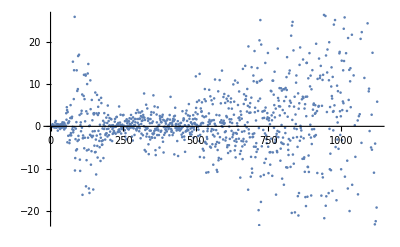

```mathematica
ListPlot[Out[27]]
```

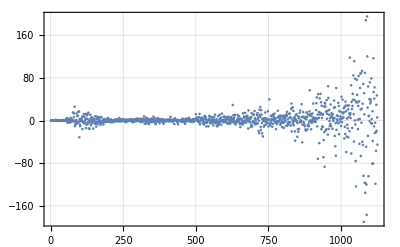

```mathematica
ListPlot[Out[27],PlotRange->Full,PlotLegends->"Expressions",PlotTheme->"Detailed",ImageSize->Full]
```

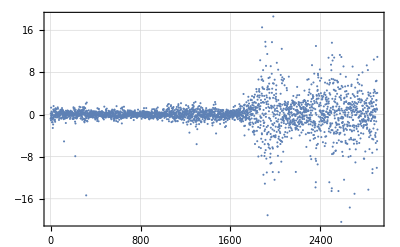

```mathematica
ListPlot[
Map[Total,
Partition[
Differences@FinancialData["NYSE:IBM","Price",All]["Values"],5]]
,PlotRange->Full,PlotLegends->"Expressions",PlotTheme->"Detailed",ImageSize->Full]
```

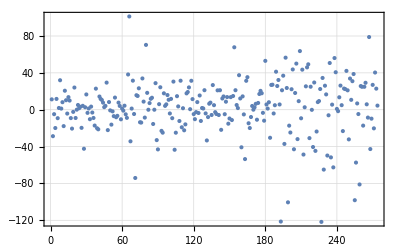

```mathematica
ListPlot[
Map[Total,
Partition[
Differences@FinancialData["NASDAQ:GOOG","Price",All]["Values"],5]]
,PlotRange->Full,PlotLegends->"Expressions",PlotTheme->"Detailed",ImageSize->Full]
```

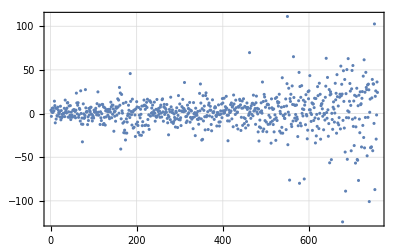

```mathematica
ListPlot[
Map[Total,
Partition[
Differences@FinancialData["NASDAQ:GOOGL","Price",All]["Values"],5]]
,PlotRange->Full,PlotLegends->"Expressions",PlotTheme->"Detailed",ImageSize->Full]
```

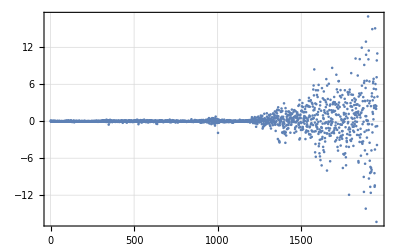

```mathematica
ListPlot[
Map[Total,
Partition[
Differences@FinancialData["NASDAQ:AAPL","Price",All]["Values"],5]]
,PlotRange->Full,PlotLegends->"Expressions",PlotTheme->"Detailed",ImageSize->Full]
```

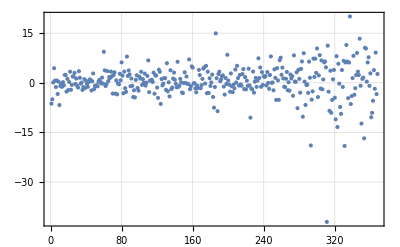

```mathematica
ListPlot[
Map[Total,
Partition[
Differences@FinancialData["NASDAQ:FB","Price",All]["Values"],5]]
,PlotRange->Full,PlotLegends->"Expressions",PlotTheme->"Detailed",ImageSize->Full]
```

```mathematica
With[{stock="NASDAQ:AAPL"},
With[{ts=FinancialData[stock,"Price",All]},
Partition[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}],5]
]]
```

{{{Fri 12 Dec 1980 00:00:00GMT-7.,-0.03 $},{Mon 15 Dec 1980 00:00:00GMT-7.,-0.04 $},{Tue 16 Dec 1980 00:00:00GMT-7.,0.01 $},{Wed 17 Dec 1980 00:00:00GMT-7.,0.01 $},{Thu 18 Dec 1980 00:00:00GMT-7.,0.03 $}},1954,{{Tue 10 Sep 2019 00:00:00GMT-7.,6.89 $},{Wed 11 Sep 2019 00:00:00GMT-7.,-0.50 $},{ | 1,-4.34 $},{ | …0GMT1,1.15 $},{Mon 16 Sep 2019 00:00:00GMT-7.,0.80 $}}}
 |  |  |  |

```mathematica
With[{stock="NASDAQ:AAPL"},
With[{ts=FinancialData[stock,"Price",All]},
Map[
Function[s,
Length@s
],Partition[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}],5]]
]]
```

{5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}

```mathematica
With[{stock="NASDAQ:AAPL"},
With[{ts=FinancialData[stock,"Price",All]},
Map[
Function[s,
s
],Partition[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}],5]]
]]
```

{{{Fri 12 Dec 1980 00:00:00GMT-7.,-0.03 $},{Mon 15 Dec 1980 00:00:00GMT-7.,-0.04 $},{Tue 16 Dec 1980 00:00:00GMT-7.,0.01 $},{Wed 17 Dec 1980 00:00:00GMT-7.,0.01 $},{Thu 18 Dec 1980 00:00:00GMT-7.,0.03 $}},1954,{{Tue 10 Sep 2019 00:00:00GMT-7.,6.89 $},{Wed 11 Sep 2019 00:00:00GMT-7.,-0.50 $},{ | 1,-4.34 $},{ | …0GMT1,1.15 $},{Mon 16 Sep 2019 00:00:00GMT-7.,0.80 $}}}
 |  |  |  |

```mathematica
With[{stock="NASDAQ:AAPL"},
With[{ts=FinancialData[stock,"Price",All]},
Map[
Function[s,
First@First@s
],Partition[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}],5]]
]]
```

{Fri 12 Dec 1980 00:00:00GMT-7.,Fri 19 Dec 1980 00:00:00GMT-7.,Mon 29 Dec 1980 00:00:00GMT-7.,Tue 6 Jan 1981 00:00:00GMT-7.,Tue 13 Jan 1981 00:00:00GMT-7.,1946,Mon 12 Aug 2019 00:00:00GMT-7.,Mon 19 Aug 2019 00:00:00GMT-7.,Mon 26 Aug 2019 00:00:00GMT-7.,Tue 3 Sep 2019 00:00:00GMT-7.,Tue 10 Sep 2019 00:00:00GMT-7.}
 |  |  |  |

```mathematica
With[{stock="NASDAQ:AAPL"},
With[{ts=FinancialData[stock,"Price",All]},
Map[
Function[s,
{First@First@s,Total@Map[Last,s]}
],Partition[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}],5]]
]]
```

{{Fri 12 Dec 1980 00:00:00GMT-7.,-0.01 $},{Fri 19 Dec 1980 00:00:00GMT-7.,0.14 $},{Mon 29 Dec 1980 00:00:00GMT-7.,-0.07 $},{Tue 6 Jan 1981 00:00:00GMT-7.,-0.03 $},{Tue 13 Jan 1981 00:00:00GMT-7.,0.02 $},1947,{Mon 19 Aug 2019 00:00:00GMT-7.,-3.86 $},{Mon 26 Aug 2019 00:00:00GMT-7.,-0.79 $},{Tue 3 Sep 2019 00:00:00GMT-7.,11.00 $},{Tue 10 Sep 2019 00:00:00GMT-7.,4.00 $}}
 |  |  |  |

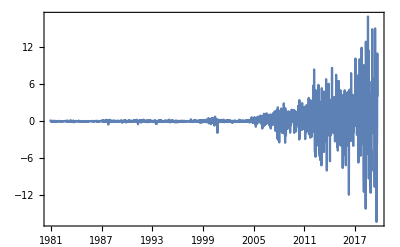

```mathematica
DateListPlot[Out[40],PlotTheme->"Detailed",PlotRange->Full,ImageSize->Full]
```

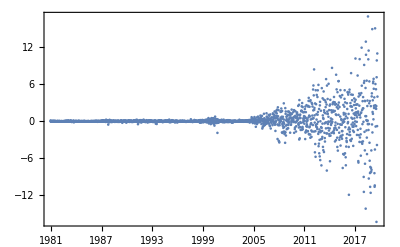

```mathematica
DateListPlot[Out[40],PlotTheme->"Detailed",PlotRange->Full,ImageSize->Full,Joined->False,ColorFunction->"DarkRainbow"]
```

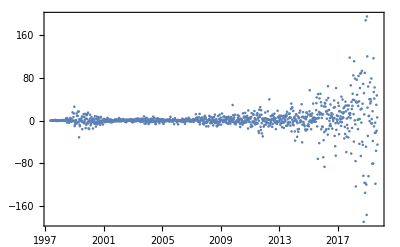

```mathematica
With[{stock="NASDAQ:AMZN"},
With[{ts=FinancialData[stock,"Price",All]},
DateListPlot[
Map[
Function[s,
{First@First@s,Total@Map[Last,s]}
],Partition[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}],5]]
,PlotTheme->"Detailed",PlotRange->Full,ImageSize->Full,Joined->False,ColorFunction->"DarkRainbow"]
]]
```

```mathematica
FinancialData["NASDAQ:AAPL","Volume"]
```

57977094 shares

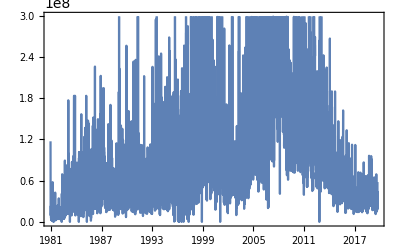

```mathematica
DateListPlot@FinancialData["NASDAQ:AAPL","Volume",All]
```

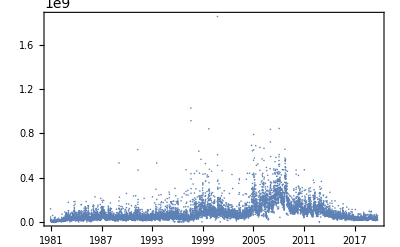

```mathematica
DateListPlot[FinancialData["NASDAQ:AAPL","Volume",All],PlotRange->Full,PlotTheme->"Detailed",Joined->False,ColorFunction->"DarkRainbow"]
```

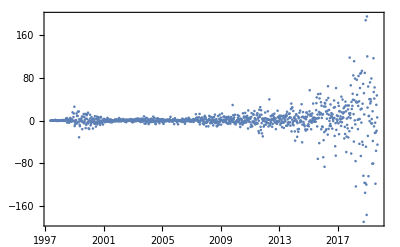

```mathematica
Show[{
With[{stock="NASDAQ:AMZN"},
With[{ts=FinancialData[stock,"Price",All]},
DateListPlot[
Map[
Function[s,
{First@First@s,Total@Map[Last,s]}
],Partition[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}],5]]
,PlotTheme->"Detailed",PlotRange->Full,ImageSize->Full,Joined->False,ColorFunction->"DarkRainbow"]
]],
DateListPlot[FinancialData["NASDAQ:AAPL","Volume",All],PlotRange->Full,PlotTheme->"Detailed",Joined->False,ColorFunction->"DarkRainbow"]
}]
```

Quantity::compat: USDollars and IndependentUnit[shares] are incompatible units

General::stop: Further output of Quantity::compat will be suppressed during this calculation.

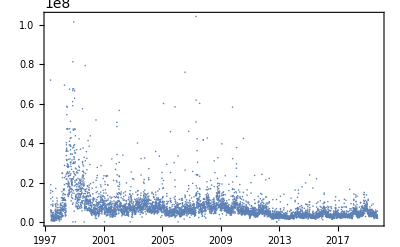

```mathematica
With[{stock="NASDAQ:AMZN"},
With[{ts=FinancialData[stock,"Price",All]},
DateListPlot[{
FinancialData[stock,"Volume",All],
Map[
Function[s,
{First@First@s,Total@Map[Last,s]}
],Partition[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}],5]]}
,PlotTheme->"Detailed",PlotRange->Full,ImageSize->Full,Joined->False,ColorFunction->"DarkRainbow"]
]]
```

```mathematica
With[{stock="NASDAQ:AMZN"},
With[{ts=FinancialData[stock,"Price",All]},
DateListPlot[{
FinancialData[stock,"Volume",All],
Map[
Function[s,
{First@First@s,Total@Map[Last,s]}
],Partition[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}],5]]}
,PlotTheme->"Detailed",PlotRange->Full,ImageSize->Full,Joined->False,PlotLegends->"Expressions"]
]]
```

Quantity::compat: USDollars and IndependentUnit[shares] are incompatible units

General::stop: Further output of Quantity::compat will be suppressed during this calculation.

-Graphics-

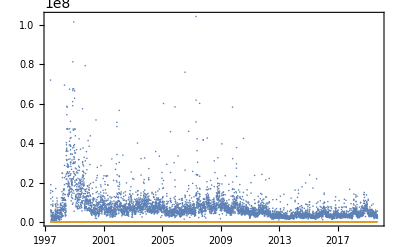

```mathematica
With[{stock="NASDAQ:AMZN"},
With[{ts=FinancialData[stock,"Price",All]},
DateListPlot[{
FinancialData[stock,"Volume",All],
Map[
Function[s,
{First@First@s,Total@Map[QuantityMagnitude@Last@#&,s]}
],Partition[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}],5]]}
,PlotTheme->"Detailed",PlotRange->Full,ImageSize->Full,Joined->False,PlotLegends->"Expressions"]
]]
```

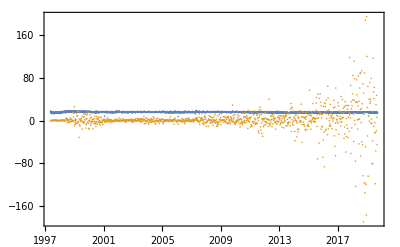

```mathematica
With[{stock="NASDAQ:AMZN"},
With[{ts=FinancialData[stock,"Price",All],vol=FinancialData[stock,"Volume",All]},
DateListPlot[{
Transpose[{
vol["Dates"],
Map[Log@QuantityMagnitude@#&,vol["Values"]]
}],
Map[
Function[s,
{First@First@s,Total@Map[QuantityMagnitude@Last@#&,s]}
],Partition[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}],5]]}
,PlotTheme->"Detailed",PlotRange->Full,ImageSize->Full,Joined->False,PlotLegends->"Expressions"]
]]
```

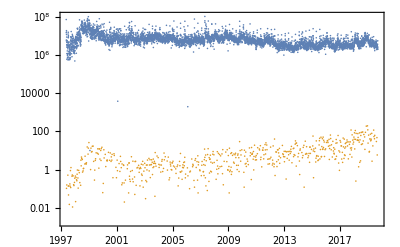

```mathematica
With[{stock="NASDAQ:AMZN"},
With[{ts=FinancialData[stock,"Price",All]},
DateListLogPlot[{
FinancialData[stock,"Volume",All],
Map[
Function[s,
{First@First@s,Total@Map[QuantityMagnitude@Last@#&,s]}
],Partition[
Transpose[{
ts["Dates"][[;;-2]],
Differences@ts["Values"]
}],5]]}
,PlotTheme->"Detailed",PlotRange->Full,ImageSize->Full,Joined->False,PlotLegends->"Expressions"]
]]
```

```mathematica
{"NASDAQ:MSFT","NASDAQ:GOOGL","NASDAQ:FB","NASDAQ:BIDU","NASDAQ:NTES","NASDAQ:VRSN","NASDAQ:MTCH","NASDAQ:IAC","NASDAQ:CRWD","NASDAQ:IQ","NASDAQ:SSNC","NASDAQ:CTXS","NASDAQ:YNDX","NASDAQ:OKTA","NASDAQ:WB","NASDAQ:DOX","NASDAQ:DBX","NASDAQ:COUP","NASDAQ:FFIV","NASDAQ:MOMO","NASDAQ:ZS","NASDAQ:WIX","NASDAQ:YY","NASDAQ:BILI","NASDAQ:NTNX","NASDAQ:JCOM","NASDAQ:CYBR","NASDAQ:ANGI","NASDAQ:CARG","NASDAQ:FIVN","NASDAQ:APPN","NASDAQ:SINA","NASDAQ:LEXEA","NASDAQ:BL","NASDAQ:LEXEB","NASDAQ:LPSN","NASDAQ:ALTR","NASDAQ:EVOP","NASDAQ:MIME","NASDAQ:TENB","NASDAQ:VRNS","NASDAQ:CSGS","NASDAQ:BAND","NASDAQ:GRPN","NASDAQ:UPWK","NASDAQ:GSKY","NASDAQ:LKCO","NASDAQ:CRTO","NASDAQ:OPRA","NASDAQ:TLND","NASDAQ:TWOU","NASDAQ:QTT","NASDAQ:UXIN","NASDAQ:SPNS","NASDAQ:CDLX","NASDAQ:JFIN","NASDAQ:LTRPA","NASDAQ:TTGT","NASDAQ:LTRPB","NASDAQ:QNST","NASDAQ:TCX","NASDAQ:EVER","NASDAQ:IIIV","NASDAQ:CARB","NASDAQ:SOHU","NASDAQ:USAT","NASDAQ:PRTH","NASDAQ:TRUE","NASDAQ:LLNW","NASDAQ:MEET","NASDAQ:TNAV","NASDAQ:XELA","NASDAQ:TC","NASDAQ:PCOM","NASDAQ:MAMS","NASDAQ:TZOO","NASDAQ:PERI","NASDAQ:CYRN","NASDAQ:VERI","NASDAQ:SREV","NASDAQ:SYNC","NASDAQ:MARK","NASDAQ:MNDO","NASDAQ:PYDS","NASDAQ:AUTO","NASDAQ:SPRT","NASDAQ:MOXC","NASDAQ:CCIH","NASDAQ:NETE","NASDAQ:DLPN","NASDAQ:IZEA","NASDAQ:IPDN"}
```

{NASDAQ:MSFT,NASDAQ:GOOGL,NASDAQ:FB,NASDAQ:BIDU,NASDAQ:NTES,NASDAQ:VRSN,NASDAQ:MTCH,NASDAQ:IAC,NASDAQ:CRWD,NASDAQ:IQ,NASDAQ:SSNC,NASDAQ:CTXS,NASDAQ:YNDX,NASDAQ:OKTA,NASDAQ:WB,NASDAQ:DOX,NASDAQ:DBX,NASDAQ:COUP,NASDAQ:FFIV,NASDAQ:MOMO,NASDAQ:ZS,NASDAQ:WIX,NASDAQ:YY,NASDAQ:BILI,NASDAQ:NTNX,NASDAQ:JCOM,NASDAQ:CYBR,NASDAQ:ANGI,NASDAQ:CARG,NASDAQ:FIVN,NASDAQ:APPN,NASDAQ:SINA,NASDAQ:LEXEA,NASDAQ:BL,NASDAQ:LEXEB,NASDAQ:LPSN,NASDAQ:ALTR,NASDAQ:EVOP,NASDAQ:MIME,NASDAQ:TENB,NASDAQ:VRNS,NASDAQ:CSGS,NASDAQ:BAND,NASDAQ:GRPN,NASDAQ:UPWK,NASDAQ:GSKY,NASDAQ:LKCO,NASDAQ:CRTO,NASDAQ:OPRA,NASDAQ:TLND,NASDAQ:TWOU,NASDAQ:QTT,NASDAQ:UXIN,NASDAQ:SPNS,NASDAQ:CDLX,NASDAQ:JFIN,NASDAQ:LTRPA,NASDAQ:TTGT,NASDAQ:LTRPB,NASDAQ:QNST,NASDAQ:TCX,NASDAQ:EVER,NASDAQ:IIIV,NASDAQ:CARB,NASDAQ:SOHU,NASDAQ:USAT,NASDAQ:PRTH,NASDAQ:TRUE,NASDAQ:LLNW,NASDAQ:MEET,NASDAQ:TNAV,NASDAQ:XELA,NASDAQ:TC,NASDAQ:PCOM,NASDAQ:MAMS,NASDAQ:TZOO,NASDAQ:PERI,NASDAQ:CYRN,NASDAQ:VERI,NASDAQ:SREV,NASDAQ:SYNC,NASDAQ:MARK,NASDAQ:MNDO,NASDAQ:PYDS,NASDAQ:AUTO,NASDAQ:SPRT,NASDAQ:MOXC,NASDAQ:CCIH,NASDAQ:NETE,NASDAQ:DLPN,NASDAQ:IZEA,NASDAQ:IPDN}

```mathematica
Grid@
ReverseSortBy[
Map[FinancialData[#,"Volume"]&,{"NASDAQ:MSFT","NASDAQ:GOOGL","NASDAQ:FB","NASDAQ:BIDU","NASDAQ:NTES","NASDAQ:VRSN","NASDAQ:MTCH","NASDAQ:IAC","NASDAQ:CRWD","NASDAQ:IQ","NASDAQ:SSNC","NASDAQ:CTXS","NASDAQ:YNDX","NASDAQ:OKTA","NASDAQ:WB","NASDAQ:DOX","NASDAQ:DBX","NASDAQ:COUP","NASDAQ:FFIV","NASDAQ:MOMO","NASDAQ:ZS","NASDAQ:WIX","NASDAQ:YY","NASDAQ:BILI","NASDAQ:NTNX","NASDAQ:JCOM","NASDAQ:CYBR","NASDAQ:ANGI","NASDAQ:CARG","NASDAQ:FIVN","NASDAQ:APPN","NASDAQ:SINA","NASDAQ:LEXEA","NASDAQ:BL","NASDAQ:LEXEB","NASDAQ:LPSN","NASDAQ:ALTR","NASDAQ:EVOP","NASDAQ:MIME","NASDAQ:TENB","NASDAQ:VRNS","NASDAQ:CSGS","NASDAQ:BAND","NASDAQ:GRPN","NASDAQ:UPWK","NASDAQ:GSKY","NASDAQ:LKCO","NASDAQ:CRTO","NASDAQ:OPRA","NASDAQ:TLND","NASDAQ:TWOU","NASDAQ:QTT","NASDAQ:UXIN","NASDAQ:SPNS","NASDAQ:CDLX","NASDAQ:JFIN","NASDAQ:LTRPA","NASDAQ:TTGT","NASDAQ:LTRPB","NASDAQ:QNST","NASDAQ:TCX","NASDAQ:EVER","NASDAQ:IIIV","NASDAQ:CARB","NASDAQ:SOHU","NASDAQ:USAT","NASDAQ:PRTH","NASDAQ:TRUE","NASDAQ:LLNW","NASDAQ:MEET","NASDAQ:TNAV","NASDAQ:XELA","NASDAQ:TC","NASDAQ:PCOM","NASDAQ:MAMS","NASDAQ:TZOO","NASDAQ:PERI","NASDAQ:CYRN","NASDAQ:VERI","NASDAQ:SREV","NASDAQ:SYNC","NASDAQ:MARK","NASDAQ:MNDO","NASDAQ:PYDS","NASDAQ:AUTO","NASDAQ:SPRT","NASDAQ:MOXC","NASDAQ:CCIH","NASDAQ:NETE","NASDAQ:DLPN","NASDAQ:IZEA","NASDAQ:IPDN"}]
,Last]
```

Grid[{40040766 shares,20359878 shares,9238700 shares,7429260 shares,6971671 shares,6179187 shares,5499649 shares,5474795 shares,5423138 shares,4740818 shares,4366247 shares,3734352 shares,3555274 shares,3374383 shares,3273122 shares,3005142 shares,2823032 shares,2673889 shares,2478701 shares,2149854 shares,2086320 shares,2078003 shares,1996704 shares,1958295 shares,1937743 shares,1927244 shares,1908437 shares,1845937 shares,1801747 shares,1781511 shares,1390764 shares,1388433 shares,1300554 shares,1291404 shares,1255808 shares,1245115 shares,1124105 shares,1107244 shares,1097142 shares,1079392 shares,1060585 shares,1033379 shares,986129 shares,952229 shares,950964 shares,914006 shares,883625 shares,837380 shares,823430 shares,819769 shares,807554 shares,802669 shares,768519 shares,684324 shares,619376 shares,536070 shares,465684 shares,413316 shares,396957 shares,395846 shares,394424 shares,379630 shares,364133 shares,359936 shares,336586 shares,314855 shares,311933 shares,310910 shares,296126 shares,217773 shares,150193 shares,144619 shares,109203 shares,71630 shares,63638 shares,63065 shares,55187 shares,49980 shares,24277 shares,22932 shares,21496 shares,21268 shares,14960 shares,13756 shares,9794 shares,7893 shares,784 shares,306 shares,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}]

```mathematica
Grid@
ReverseSortBy[
Map[
{#,FinancialData[#,"Volume"]}&
,{"NASDAQ:MSFT","NASDAQ:GOOGL","NASDAQ:FB","NASDAQ:BIDU","NASDAQ:NTES","NASDAQ:VRSN","NASDAQ:MTCH","NASDAQ:IAC","NASDAQ:CRWD","NASDAQ:IQ","NASDAQ:SSNC","NASDAQ:CTXS","NASDAQ:YNDX","NASDAQ:OKTA","NASDAQ:WB","NASDAQ:DOX","NASDAQ:DBX","NASDAQ:COUP","NASDAQ:FFIV","NASDAQ:MOMO","NASDAQ:ZS","NASDAQ:WIX","NASDAQ:YY","NASDAQ:BILI","NASDAQ:NTNX","NASDAQ:JCOM","NASDAQ:CYBR","NASDAQ:ANGI","NASDAQ:CARG","NASDAQ:FIVN","NASDAQ:APPN","NASDAQ:SINA","NASDAQ:LEXEA","NASDAQ:BL","NASDAQ:LEXEB","NASDAQ:LPSN","NASDAQ:ALTR","NASDAQ:EVOP","NASDAQ:MIME","NASDAQ:TENB","NASDAQ:VRNS","NASDAQ:CSGS","NASDAQ:BAND","NASDAQ:GRPN","NASDAQ:UPWK","NASDAQ:GSKY","NASDAQ:LKCO","NASDAQ:CRTO","NASDAQ:OPRA","NASDAQ:TLND","NASDAQ:TWOU","NASDAQ:QTT","NASDAQ:UXIN","NASDAQ:SPNS","NASDAQ:CDLX","NASDAQ:JFIN","NASDAQ:LTRPA","NASDAQ:TTGT","NASDAQ:LTRPB","NASDAQ:QNST","NASDAQ:TCX","NASDAQ:EVER","NASDAQ:IIIV","NASDAQ:CARB","NASDAQ:SOHU","NASDAQ:USAT","NASDAQ:PRTH","NASDAQ:TRUE","NASDAQ:LLNW","NASDAQ:MEET","NASDAQ:TNAV","NASDAQ:XELA","NASDAQ:TC","NASDAQ:PCOM","NASDAQ:MAMS","NASDAQ:TZOO","NASDAQ:PERI","NASDAQ:CYRN","NASDAQ:VERI","NASDAQ:SREV","NASDAQ:SYNC","NASDAQ:MARK","NASDAQ:MNDO","NASDAQ:PYDS","NASDAQ:AUTO","NASDAQ:SPRT","NASDAQ:MOXC","NASDAQ:CCIH","NASDAQ:NETE","NASDAQ:DLPN","NASDAQ:IZEA","NASDAQ:IPDN"}],Last]
```

NASDAQ:MSFT | 40040766 shares
NASDAQ:FB | 20359878 shares
NASDAQ:GRPN | 9238700 shares
NASDAQ:USAT | 7429260 shares
NASDAQ:ZS | 6971671 shares
NASDAQ:DBX | 6179187 shares
NASDAQ:QTT | 5499649 shares
NASDAQ:OKTA | 5474795 shares
NASDAQ:IQ | 5423138 shares
NASDAQ:YNDX | 4740818 shares
NASDAQ:TRUE | 4366247 shares
NASDAQ:TWOU | 3734352 shares
NASDAQ:BIDU | 3555274 shares
NASDAQ:CRWD | 3374383 shares
NASDAQ:CTXS | 3273122 shares
NASDAQ:NTNX | 3005142 shares
NASDAQ:BILI | 2823032 shares
NASDAQ:QNST | 2673889 shares
NASDAQ:CARG | 2478701 shares
NASDAQ:CARB | 2149854 shares
NASDAQ:OPRA | 2086320 shares
NASDAQ:TENB | 2078003 shares
NASDAQ:MOMO | 1996704 shares
NASDAQ:WB | 1958295 shares
NASDAQ:GOOGL | 1937743 shares
NASDAQ:MTCH | 1927244 shares
NASDAQ:ANGI | 1908437 shares
NASDAQ:UPWK | 1845937 shares
NASDAQ:UXIN | 1801747 shares
NASDAQ:COUP | 1781511 shares
NASDAQ:SSNC | 1390764 shares
NASDAQ:TNAV | 1388433 shares
NASDAQ:ALTR | 1300554 shares
NASDAQ:APPN | 1291404 shares
NASDAQ:LLNW | 1255808 shares
NASDAQ:MEET | 1245115 shares
NASDAQ:IAC | 1124105 shares
NASDAQ:YY | 1107244 shares
NASDAQ:SINA | 1097142 shares
NASDAQ:EVOP | 1079392 shares
NASDAQ:IZEA | 1060585 shares
NASDAQ:BL | 1033379 shares
NASDAQ:LPSN | 986129 shares
NASDAQ:GSKY | 952229 shares
NASDAQ:FIVN | 950964 shares
NASDAQ:CYBR | 914006 shares
NASDAQ:JCOM | 883625 shares
NASDAQ:VRSN | 837380 shares
NASDAQ:LKCO | 823430 shares
NASDAQ:MIME | 819769 shares
NASDAQ:DOX | 807554 shares
NASDAQ:IIIV | 802669 shares
NASDAQ:LTRPA | 768519 shares
NASDAQ:FFIV | 684324 shares
NASDAQ:NTES | 619376 shares
NASDAQ:CRTO | 536070 shares
NASDAQ:CSGS | 465684 shares
NASDAQ:TTGT | 413316 shares
NASDAQ:WIX | 396957 shares
NASDAQ:BAND | 395846 shares
NASDAQ:SREV | 394424 shares
NASDAQ:VERI | 379630 shares
NASDAQ:SYNC | 364133 shares
NASDAQ:MARK | 359936 shares
NASDAQ:VRNS | 336586 shares
NASDAQ:EVER | 314855 shares
NASDAQ:CDLX | 311933 shares
NASDAQ:SOHU | 310910 shares
NASDAQ:PERI | 296126 shares
NASDAQ:TLND | 217773 shares
NASDAQ:XELA | 150193 shares
NASDAQ:SPNS | 144619 shares
NASDAQ:TZOO | 109203 shares
NASDAQ:TCX | 71630 shares
NASDAQ:NETE | 63638 shares
NASDAQ:MAMS | 63065 shares
NASDAQ:PRTH | 55187 shares
NASDAQ:SPRT | 49980 shares
NASDAQ:PCOM | 24277 shares
NASDAQ:JFIN | 22932 shares
NASDAQ:PYDS | 21496 shares
NASDAQ:TC | 21268 shares
NASDAQ:AUTO | 14960 shares
NASDAQ:MNDO | 13756 shares
NASDAQ:CYRN | 9794 shares
NASDAQ:DLPN | 7893 shares
NASDAQ:IPDN | 784 shares
NASDAQ:MOXC | 306 shares
NASDAQ:LTRPB | Missing[NotAvailable]
NASDAQ:LEXEB | Missing[NotAvailable]
NASDAQ:LEXEA | Missing[NotAvailable]
NASDAQ:CCIH | Missing[NotAvailable]

```mathematica
Grid@
ReverseSortBy[
Map[
{#,FinancialData[#,"Volume"],FinancialData[#,"MarketCap"]}&
,{"NASDAQ:MSFT","NASDAQ:GOOGL","NASDAQ:FB","NASDAQ:BIDU","NASDAQ:NTES","NASDAQ:VRSN","NASDAQ:MTCH","NASDAQ:IAC","NASDAQ:CRWD","NASDAQ:IQ","NASDAQ:SSNC","NASDAQ:CTXS","NASDAQ:YNDX","NASDAQ:OKTA","NASDAQ:WB","NASDAQ:DOX","NASDAQ:DBX","NASDAQ:COUP","NASDAQ:FFIV","NASDAQ:MOMO","NASDAQ:ZS","NASDAQ:WIX","NASDAQ:YY","NASDAQ:BILI","NASDAQ:NTNX","NASDAQ:JCOM","NASDAQ:CYBR","NASDAQ:ANGI","NASDAQ:CARG","NASDAQ:FIVN","NASDAQ:APPN","NASDAQ:SINA","NASDAQ:LEXEA","NASDAQ:BL","NASDAQ:LEXEB","NASDAQ:LPSN","NASDAQ:ALTR","NASDAQ:EVOP","NASDAQ:MIME","NASDAQ:TENB","NASDAQ:VRNS","NASDAQ:CSGS","NASDAQ:BAND","NASDAQ:GRPN","NASDAQ:UPWK","NASDAQ:GSKY","NASDAQ:LKCO","NASDAQ:CRTO","NASDAQ:OPRA","NASDAQ:TLND","NASDAQ:TWOU","NASDAQ:QTT","NASDAQ:UXIN","NASDAQ:SPNS","NASDAQ:CDLX","NASDAQ:JFIN","NASDAQ:LTRPA","NASDAQ:TTGT","NASDAQ:LTRPB","NASDAQ:QNST","NASDAQ:TCX","NASDAQ:EVER","NASDAQ:IIIV","NASDAQ:CARB","NASDAQ:SOHU","NASDAQ:USAT","NASDAQ:PRTH","NASDAQ:TRUE","NASDAQ:LLNW","NASDAQ:MEET","NASDAQ:TNAV","NASDAQ:XELA","NASDAQ:TC","NASDAQ:PCOM","NASDAQ:MAMS","NASDAQ:TZOO","NASDAQ:PERI","NASDAQ:CYRN","NASDAQ:VERI","NASDAQ:SREV","NASDAQ:SYNC","NASDAQ:MARK","NASDAQ:MNDO","NASDAQ:PYDS","NASDAQ:AUTO","NASDAQ:SPRT","NASDAQ:MOXC","NASDAQ:CCIH","NASDAQ:NETE","NASDAQ:DLPN","NASDAQ:IZEA","NASDAQ:IPDN"}],Last]
```

NASDAQ:MSFT | 40040766 shares | 1.0771272599814087e12 $
NASDAQ:GOOGL | 1937743 shares | 8.589472060625e11 $
NASDAQ:FB | 20359878 shares | 5.4246000594841724e11 $
NASDAQ:BIDU | 3555274 shares | 3.756222791357208e10 $
NASDAQ:NTES | 619376 shares | 3.470679183109863e10 $
NASDAQ:VRSN | 837380 shares | 2.2619676000829346e10 $
NASDAQ:MTCH | 1927244 shares | 2.226470824348591e10 $
NASDAQ:IAC | 1124105 shares | 1.9642486225932312e10 $
NASDAQ:CRWD | 3374383 shares | 1.4130545633610573e10 $
NASDAQ:IQ | 5423138 shares | 1.3806487306713776e10 $
NASDAQ:SSNC | 1390764 shares | 1.282755749419664e10 $
NASDAQ:CTXS | 3273122 shares | 1.2625508399368454e10 $
NASDAQ:YNDX | 4740818 shares | 1.2239081263073158e10 $
NASDAQ:OKTA | 5474795 shares | 1.1813393952e10 $
NASDAQ:WB | 1958295 shares | 1.1118979315662384e10 $
NASDAQ:DOX | 807554 shares | 9.065155065589905e9 $
NASDAQ:DBX | 6179187 shares | 8.693494278469196e9 $
NASDAQ:COUP | 1781511 shares | 8.52683902275914e9 $
NASDAQ:FFIV | 684324 shares | 8.309968718697739e9 $
NASDAQ:MOMO | 1996704 shares | 7.549510191128693e9 $
NASDAQ:ZS | 6971671 shares | 6.327077883055115e9 $
NASDAQ:WIX | 396957 shares | 6.160528953518692e9 $
NASDAQ:YY | 1107244 shares | 5.034772514551979e9 $
NASDAQ:BILI | 2823032 shares | 4.924463494606205e9 $
NASDAQ:NTNX | 3005142 shares | 4.918603657125111e9 $
NASDAQ:JCOM | 883625 shares | 4.487668777461472e9 $
NASDAQ:CYBR | 914006 shares | 3.967739794e9 $
NASDAQ:ANGI | 1908437 shares | 3.7601482992304306e9 $
NASDAQ:CARG | 2478701 shares | 3.7245839131816864e9 $
NASDAQ:FIVN | 950964 shares | 3.517660618e9 $
NASDAQ:APPN | 1291404 shares | 3.0865420401789093e9 $
NASDAQ:SINA | 1097142 shares | 3.031113373935074e9 $
NASDAQ:LEXEA | Missing[NotAvailable] | 2.8770432465171814e9 $
NASDAQ:BL | 1033379 shares | 2.757247441801464e9 $
NASDAQ:LEXEB | Missing[NotAvailable] | 2.7332483320690155e9 $
NASDAQ:LPSN | 986129 shares | 2.518232912837494e9 $
NASDAQ:ALTR | 1300554 shares | 2.4742957274444046e9 $
NASDAQ:EVOP | 1079392 shares | 2.410602459761656e9 $
NASDAQ:MIME | 819769 shares | 2.3536499713849335e9 $
NASDAQ:TENB | 2078003 shares | 2.342358219162903e9 $
NASDAQ:VRNS | 336586 shares | 1.8982787829578056e9 $
NASDAQ:CSGS | 465684 shares | 1.76723218113945e9 $
NASDAQ:BAND | 395846 shares | 1.6842958034458923e9 $
NASDAQ:GRPN | 9238700 shares | 1.6177167292675457e9 $
NASDAQ:UPWK | 1845937 shares | 1.570088564983652e9 $
NASDAQ:GSKY | 952229 shares | 1.33714207408008e9 $
NASDAQ:LKCO | 823430 shares | 1.3180895163569832e9 $
NASDAQ:CRTO | 536070 shares | 1.271492273016529e9 $
NASDAQ:OPRA | 2086320 shares | 1.2076553638142023e9 $
NASDAQ:TLND | 217773 shares | 1.2052467747640228e9 $
NASDAQ:TWOU | 3734352 shares | 1.127994374885519e9 $
NASDAQ:QTT | 5499649 shares | 1.1071658837451553e9 $
NASDAQ:UXIN | 1801747 shares | 9.217573896549666e8 $
NASDAQ:SPNS | 144619 shares | 9.041744599866486e8 $
NASDAQ:CDLX | 311933 shares | 8.111214412403641e8 $
NASDAQ:JFIN | 22932 shares | 7.383000102043152e8 $
NASDAQ:LTRPA | 768519 shares | 7.169816111697264e8 $
NASDAQ:TTGT | 413316 shares | 6.896427153878002e8 $
NASDAQ:LTRPB | Missing[NotAvailable] | 6.88242278334753e8 $
NASDAQ:QNST | 2673889 shares | 6.264022155210495e8 $
NASDAQ:TCX | 71630 shares | 5.925701916157608e8 $
NASDAQ:EVER | 314855 shares | 5.783146074223022e8 $
NASDAQ:IIIV | 802669 shares | 5.666518051415768e8 $
NASDAQ:CARB | 2149854 shares | 5.2138636209684753e8 $
NASDAQ:SOHU | 310910 shares | 4.7427303040579987e8 $
NASDAQ:USAT | 7429260 shares | 4.103769493658948e8 $
NASDAQ:PRTH | 55187 shares | 3.9601237629551697e8 $
NASDAQ:TRUE | 4366247 shares | 3.907597141285937e8 $
NASDAQ:LLNW | 1255808 shares | 3.6254739374184036e8 $
NASDAQ:MEET | 1245115 shares | 2.6156368628074622e8 $
NASDAQ:TNAV | 1388433 shares | 2.4367141583432007e8 $
NASDAQ:XELA | 150193 shares | 2.025095683264476e8 $
NASDAQ:TC | 21268 shares | 1.8803940830275536e8 $
NASDAQ:PCOM | 24277 shares | 1.586224867044983e8 $
NASDAQ:MAMS | 63065 shares | 1.5175092788159847e8 $
NASDAQ:TZOO | 109203 shares | 1.2979766536452675e8 $
NASDAQ:PERI | 296126 shares | 1.2224685873899174e8 $
NASDAQ:CYRN | 9794 shares | 9.539478725e7 $
NASDAQ:VERI | 379630 shares | 8.844934336387873e7 $
NASDAQ:SREV | 394424 shares | 8.467414065690124e7 $
NASDAQ:SYNC | 364133 shares | 5.553457926436615e7 $
NASDAQ:MARK | 359936 shares | 5.496869585425079e7 $
NASDAQ:MNDO | 13756 shares | 4.628676106567192e7 $
NASDAQ:PYDS | 21496 shares | 3.6334283192173004e7 $
NASDAQ:AUTO | 14960 shares | 3.299854568462205e7 $
NASDAQ:SPRT | 49980 shares | 2.9211874276399612e7 $
NASDAQ:MOXC | 306 shares | 2.6538912515423536e7 $
NASDAQ:CCIH | Missing[NotAvailable] | 2.354860623193556e7 $
NASDAQ:NETE | 63638 shares | 2.2195361870203972e7 $
NASDAQ:DLPN | 7893 shares | 1.0719342146255374e7 $
NASDAQ:IZEA | 1060585 shares | 1.0395458452732265e7 $
NASDAQ:IPDN | 784 shares | 7.3213375e6 $

```mathematica
FinancialData["NASDAQ:MSFT","Price"]
```

Missing[NotAvailable]

```mathematica
FinancialData["NASDAQ:MSFT","PERatio"]
```

27.2877

```mathematica
Grid@
Map[
{#,FinancialData["NASDAQ:MSFT",#]}&,
FinancialData["NASDAQ:MSFT","Properties"]
]
```

AdjustedClose | Missing[NotAvailable]
AdjustedHigh | Missing[NotAvailable]
AdjustedLow | Missing[NotAvailable]
AdjustedOHLC | Missing[NotAvailable]
AdjustedOHLCV | {Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],40040766 shares}
AdjustedOpen | Missing[NotAvailable]
AdjustedRange | Missing[NotAvailable]
Ask | Missing[NotAvailable]
AskSize | Missing[NotAvailable]
Average200Day | 122.48 $
Average50Day | 137.44 $
AverageVolume3Month | 2.43379×10^7 shares
Bid | Missing[NotAvailable]
BidSize | Missing[NotAvailable]
BookValuePerShare | Missing[NotAvailable]
Change | Missing[NotAvailable]
Change200Day | Missing[NotAvailable]
Change50Day | Missing[NotAvailable]
ChangeHigh52Week | Missing[NotAvailable]
ChangeLow52Week | Missing[NotAvailable]
CIK | 0000789019
Close | 139.44 $
Company | Microsoft
CumulativeFractionalChange | Missing[NotAvailable]
CumulativeReturn | Missing[NotAvailable]
Dividend | Missing[NotAvailable]
DividendPerShare | Missing[NotAvailable]
DividendYield | Missing[NotAvailable]
EarningsPerShare | 5.11 $
EarningsYield | 3.66466 %
EBITDA | 54641000000 $
Exchange | Nasdaq
FloatShares | 7635409400
FractionalChange | Missing[NotAvailable]
FractionalChange200Day | Missing[NotAvailable]
FractionalChange50Day | Missing[NotAvailable]
FractionalChangeHigh52Week | Missing[NotAvailable]
FractionalChangeLow52Week | Missing[NotAvailable]
High | 141.65 $
High52Week | 142.37 $
IPODate | Day: Thu 13 Mar 1986
Last | Missing[NotAvailable]
LastTradeSize | Missing[NotAvailable]
LatestTrade | {Fri 20 Sep 2019 00:00:00GMT-4.,139.44 $}
Lookup | {NASDAQ:MSFT}
Low | 138.25 $
Low52Week | 93.96 $
MarketCap | 1.0771272599814087e12 $
Members | Missing[NotAvailable]
Name | Microsoft
OHLC | {141.01 $,141.65 $,138.25 $,139.44 $}
OHLCV | {141.01 $,141.65 $,138.25 $,139.44 $,40040766 shares}
Open | 141.01 $
PERatio | 27.2877
Price | Missing[NotAvailable]
PriceToBookRatio | Missing[NotAvailable]
PriceToSalesRatio | Missing[NotAvailable]
Properties | {AdjustedClose,AdjustedHigh,AdjustedLow,AdjustedOHLC,AdjustedOHLCV,AdjustedOpen,AdjustedRange,Ask,AskSize,Average200Day,Average50Day,AverageVolume3Month,Bid,BidSize,BookValuePerShare,Change,Change200Day,Change50Day,ChangeHigh52Week,ChangeLow52Week,CIK,Close,Company,CumulativeFractionalChange,CumulativeReturn,Dividend,DividendPerShare,DividendYield,EarningsPerShare,EarningsYield,EBITDA,Exchange,FloatShares,FractionalChange,FractionalChange200Day,FractionalChange50Day,FractionalChangeHigh52Week,FractionalChangeLow52Week,High,High52Week,IPODate,Last,LastTradeSize,LatestTrade,Lookup,Low,Low52Week,MarketCap,Members,Name,OHLC,OHLCV,Open,PERatio,Price,PriceToBookRatio,PriceToSalesRatio,Properties,Range,Range52Week,RawClose,RawHigh,RawLow,RawOHLC,RawOHLCV,RawOpen,RawRange,RawVolume,Return,Sector,SICCode,StandardName,Symbol,Volatility20Day,Volatility250Day,Volatility50Day,Volume,Website}
Range | {138.25 $,141.65 $}
Range52Week | {93.96 $,142.37 $}
RawClose | Missing[NotAvailable]
RawHigh | Missing[NotAvailable]
RawLow | Missing[NotAvailable]
RawOHLC | Missing[NotAvailable]
RawOHLCV | Missing[NotAvailable]
RawOpen | Missing[NotAvailable]
RawRange | Missing[NotAvailable]
RawVolume | Missing[NotAvailable]
Return | Missing[NotAvailable]
Sector | Software-Infrastructure
SICCode | 7372
StandardName | NASDAQ:MSFT
Symbol | NASDAQ:MSFT
Volatility20Day | Missing[NotAvailable]
Volatility250Day | Missing[NotAvailable]
Volatility50Day | Missing[NotAvailable]
Volume | 40040766 shares
Website | http://www.microsoft.com